## Some definitions

```mathematica
Swap[m_,i_,j_]:=Block[{c=m},

c[[All,{i,j}]]=c[[All,{j,i}]];
c[[{i,j}]]=c[[{j,i}]];
c
]
```

```mathematica
Swap2[m_,i_,j_]:=Block[{c=m, temp},
temp=c[[j]];
c[[j]]=c[[i]];
c[[i]]=temp;
c
]
```

```mathematica
ContractMat[mat_, row_, col_]:=Block[{ matJoin, matContract,fromVertexToVertexSet,vertexSets,rowBucket,colBucket, max, max2, size},
size=Length[mat];
vertexSets=Table[{i},{i,size}];
If[mat[[row,col]]==0,
matJoin=mat;
matContract=mat;

(* first compute to which vertex set row and column belong*)
fromVertexToVertexSet=Association[];
Table[Table[fromVertexToVertexSet[v]=k,{v,vertexSets[[k]]}],{k,Length[vertexSets]}];
rowBucket=vertexSets[[fromVertexToVertexSet[row]]];
colBucket=vertexSets[[fromVertexToVertexSet[col]]];

(* now set the entries in contract and joined *)
Table[
matContract[[r,c]]=2;
matContract[[c,r]]=2;
matJoin[[r,c]]=1;
matJoin[[c,r]]=1
,
{r,rowBucket},
{c,colBucket}
];
(* now make sure the entries are consistent.  We take the max of the other entries *)
Table[
max=Max[Table[matContract[[r,v]],{r, rowBucket}]];
max2=Max[Table[matContract[[r,v]],{r, colBucket}]];
max=Max[max,max2];
Table[matContract[[r,v]]=max;matContract[[v,r]]=max,{r, rowBucket}];
Table[matContract[[r,v]]=max;matContract[[v,r]]=max,{r, colBucket}];
,
{v,size}
];

];
matContract
]
```

## Now for the calculations

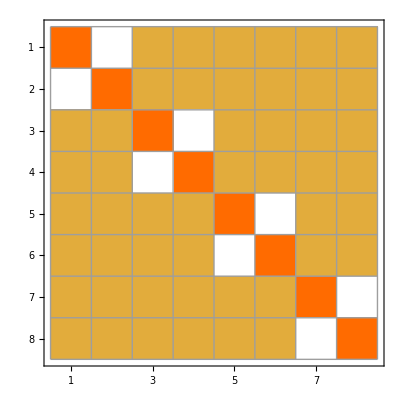
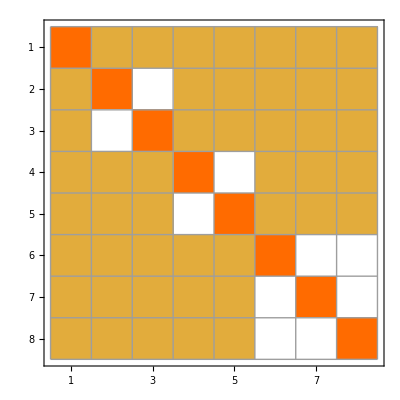
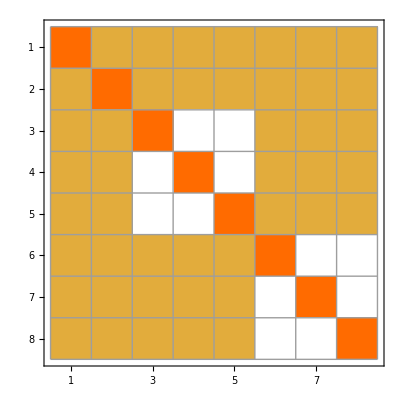
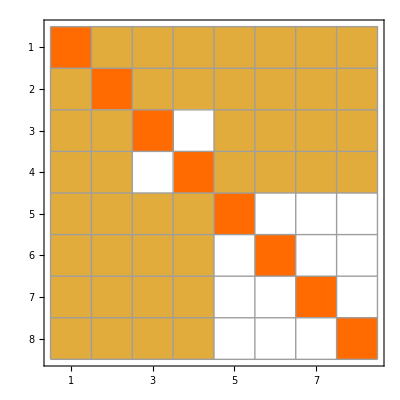
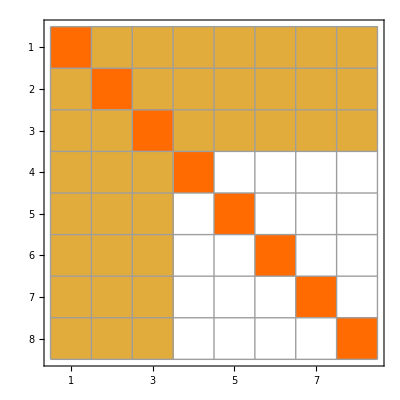

```mathematica
Map[With[{g=#},Block[{m,size=6},
m=MatrixFromGraph[g];
size=6;
MatrixPlot[ m,Mesh->All]]]&,BarelyFourColorableGraphsOfCount[8]]//Sort
```

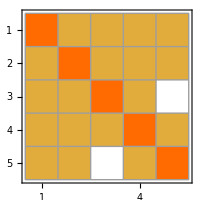

```mathematica
With[{g=MinimalGraph[4]},Block[{m,size=6},
m=MatrixFromGraph[g];
size=6;
MatrixPlot[ m,Mesh->All, ImageSize->200]]]
```

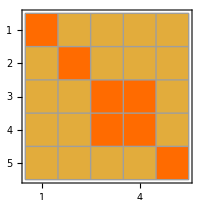

```mathematica
With[{g=MinimalGraph[4]},Block[{m,size=6},
m=MatrixFromGraph[g];
size=6;
MatrixPlot[ Swap[ContractMat[m,3,5],4,5],Mesh->All, ImageSize->200]
]
]
```

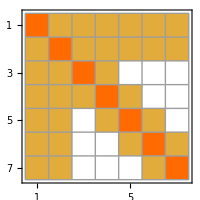

```mathematica
With[{g=MinimalGraph[6]},Block[{m,size=6},
m=MatrixFromGraph[g];
size=6;
MatrixPlot[ m,Mesh->All, ImageSize->200]
]
]
```

```mathematica
v1x2x357x46
```

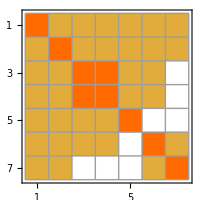

```mathematica
With[{g=MinimalGraph[6]},Block[{m},
m=MatrixFromGraph[g];
m=ContractMat[m,3,5];
m=Swap[m,4,5];
MatrixPlot[ m,Mesh->All, ImageSize->200]
]
]
```

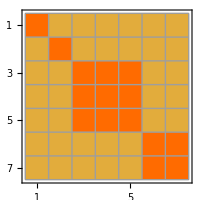

```mathematica
With[{g=MinimalGraph[6]},Block[{m,size=6},
m=MatrixFromGraph[g];
size=6;
m=ContractMat[m,3,5];
m=ContractMat[m,3,7];
m=ContractMat[m,4,6];
m=Swap[m,4,7];
MatrixPlot[ m,Mesh->All, ImageSize->200]
]
]
```

## Plantri8 has some more

```mathematica
Take[FindFullFormula4[plantri8],10]
```

{v14acx29bdx357hx68efg,v14acx259dx37bhx68efg,v137gx24acx568fx9bdeh,v14acx259dfx37ghx68be,v14acx259dfx37bhx68eg,v14adx29bcx357hx68efg,v14adx259cx37bhx68efg,v137gx258acx4bdhx69ef,v137gx258acx46fx9bdeh,v1467x258acx3fgx9bdeh}

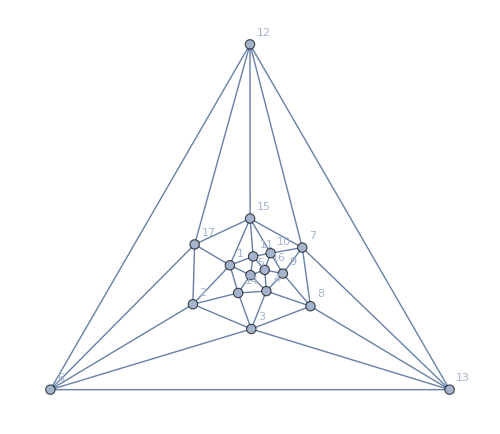
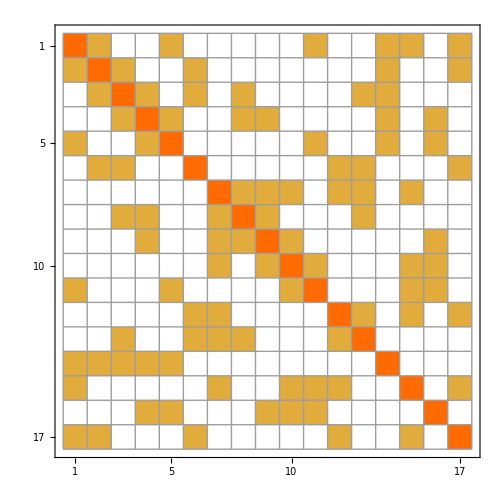

```mathematica
With[{g=plantri8},Block[{m,size=6},
m=MatrixFromGraph[g];
size=6;
{Graph[g,ImageSize->500],MatrixPlot[ m,Mesh->All, ImageSize->500]}
]
]
```

```mathematica
perm=Block[{res=Range[17]},
res=Swap2[res,6,13];
res=Swap2[res,8,17];


res=Swap2[res,3,12];
res=Swap2[res,8,11];
res=Swap2[res,7,10];
res=Swap2[res,5,9];


res=Swap2[res,2,7];
res
]
```

{1,10,12,4,9,13,2,11,5,7,17,3,6,14,15,16,8}

```mathematica
PermissionsGroup
```

```mathematica
SymbolToSets[v14acx29bdx357hx68efg]
```

{{1,4,10,12},{2,9,11,13},{3,5,7,17},{6,8,14,15,16}}

```mathematica
SymbolToSets[v14acx29bdx357hx68efg]
```

{{1,4,10,12},{2,9,11,13},{3,5,7,17},{6,8,14,15,16}}

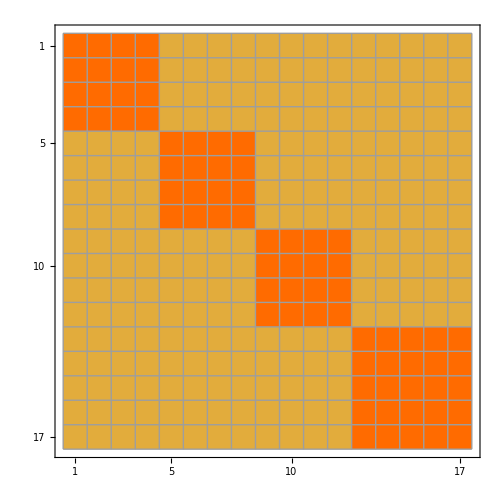
{-Graphics-,-Graphics-}

```mathematica
With[{g=plantri8},Block[{m},
m=MatrixFromGraph[g];
m=ContractMat[m,1,4];
m=ContractMat[m,1,10];
m=ContractMat[m,1,12];

m=ContractMat[m,2,9];
m=ContractMat[m,2,11];
m=ContractMat[m,2,13];

m=ContractMat[m,3,5];
m=ContractMat[m,3,7];
m=ContractMat[m,3,17];

m=ContractMat[m,6,8];
m=ContractMat[m,6,14];
m=ContractMat[m,6,15];
m=ContractMat[m,6,16];


m=Swap[m,6,13];
m=Swap[m,8,17];


m=Swap[m,3,12];
m=Swap[m,8,11];
m=Swap[m,7,10];
m=Swap[m,5,9];


m=Swap[m,2,7];

{Graph[g,ImageSize->500],MatrixPlot[ m,Mesh->All, ImageSize->500]}
]
]
```

```mathematica
SymbolToSets[v14acx29bdx357hx68efg]
```

{{1,4,10,12},{2,9,11,13},{3,5,7,17},{6,8,14,15,16}}

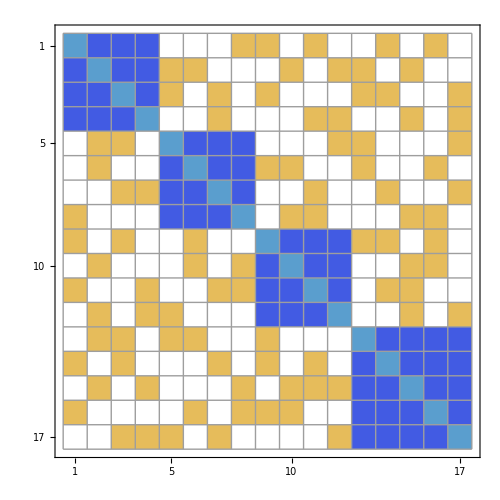
{-Graphics-,-Graphics-}

```mathematica
With[{g=plantri8},Block[{m},
m=MatrixFromGraph[g];

m=Swap[m,6,17];
m=Swap[m,8,13];
m[[13;;17,13;;17]]-=3;

m=Swap[m,1,11];
m=Swap[m,4,9];
m[[9;;12,9;;12]]-=3;


m=Swap[m,1,8];
m=Swap[m,2,7];
m=Swap[m,4,6];
m=Swap[m,1,5];
m[[5;;8,5;;8]]-=3;


m[[1;;4,1;;4]]-=3;
{Graph[g,ImageSize->500],MatrixPlot[ m,Mesh->All, ImageSize->500]}
]
]
```

```mathematica
SymbolToColoring[v14acx29bdx357hx68efg]
```

{1→RGBColor[1, 0, 0],4→RGBColor[1, 0, 0],10→RGBColor[1, 0, 0],12→RGBColor[1, 0, 0],2→RGBColor[0, 0, 1],9→RGBColor[0, 0, 1],11→RGBColor[0, 0, 1],13→RGBColor[0, 0, 1],3→RGBColor[1, 1, 0],5→RGBColor[1, 1, 0],7→RGBColor[1, 1, 0],17→RGBColor[1, 1, 0],6→RGBColor[0, 1, 0],8→RGBColor[0, 1, 0],14→RGBColor[0, 1, 0],15→RGBColor[0, 1, 0],16→RGBColor[0, 1, 0]}

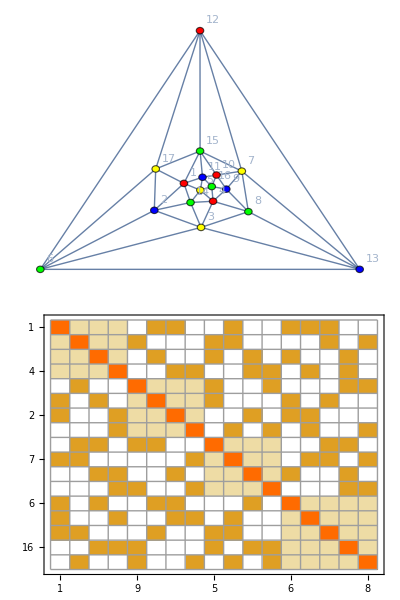

```mathematica
With[{g=plantri8},Block[{m, labels, colors=SymbolToColoring[v14acx29bdx357hx68efg]},
labels=Table[{k,Block[{res=Style[perm[[k]],Darker[(perm[[k]]/.colors)]]},
res=If[perm[[k]]==14,Framed[Style[res,Bold]],res];
res]},{k,17}];
m=MatrixFromGraph[g];

m=Swap[m,1,4];
m=Swap[m,1,10];
m=Swap[m,1,12];

m=Swap[m,2,9];
m=Swap[m,2,11];
m=Swap[m,2,13];

m=Swap[m,3,5];
m=Swap[m,3,7];
m=Swap[m,3,17];

m=Swap[m,6,8];
m=Swap[m,6,14];
m=Swap[m,6,15];
m=Swap[m,6,16];

m=Swap[m,6,17];
m=Swap[m,8,13];

m=Swap[m,1,11];
m=Swap[m,4,9];


m=Swap[m,1,8];
m=Swap[m,2,7];
m=Swap[m,4,6];
m=Swap[m,1,5];


m[[1;;4,1;;4]]+=.1;
m[[13;;17,13;;17]]+=.1;
m[[9;;12,9;;12]]+=.1;
m[[5;;8,5;;8]]+=.1;
Column[{Graph[g,ImageSize->500,VertexStyle->colors],MatrixPlot[ m,Mesh->All, ImageSize->500,FrameTicks->{labels,labels,labels,labels}]}]
]
]
```